## Import numerical data

```mathematica
(* import τ as a function of q *)
τq1=Import[NotebookDirectory[]<>"data/tauqmu_rho_1.dat"];
τq09=Import[NotebookDirectory[]<>"data/tauqmu_rho_09.dat"];
τq08=Import[NotebookDirectory[]<>"data/tauqmu_rho_08.dat"];
τq07=Import[NotebookDirectory[]<>"data/tauqmu_rho_07.dat"];
τq06=Import[NotebookDirectory[]<>"data/tauqmu_rho_06.dat"];
τq05=Import[NotebookDirectory[]<>"data/tauqmu_rho_05.dat"];
τq04=Import[NotebookDirectory[]<>"data/tauqmu_rho_04.dat"];
τq03=Import[NotebookDirectory[]<>"data/tauqmu_rho_03.dat"];
τq02=Import[NotebookDirectory[]<>"data/tauqmu_rho_02.dat"];
τq01=Import[NotebookDirectory[]<>"data/tauqmu_rho_01.dat"];
```

```mathematica
(*τpython=Import[NotebookDirectory[]<>"data/tauqpsi_python_rho_0.5_n_14.dat"];*)
τpython01=Import[NotebookDirectory[]<>"data/tauqpsi_python_rho_0.1_n_16.dat"];
τpython01test=Import[NotebookDirectory[]<>"data/tauqpsi_python_rho_0.1_n_16_test.dat"];
τpython05test=Import[NotebookDirectory[]<>"data/tauqpsi_python_rho_0.5_n_16_test.dat"];
```

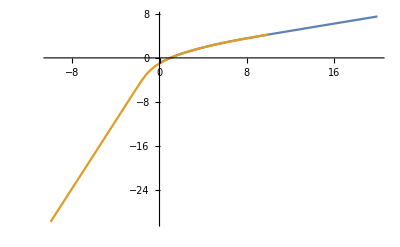

```mathematica
ListPlot[{τq05,τpython05test},Joined->True]
```

```mathematica
τs={τq1,τq09,τq08,τq07,τq06,τq05,τq04,τq03,τq02,τq01};
```

## Legendre transform of τ_q ⟶ f-α graph

```mathematica
legendre[τq_]:=Block[{τinterp,α},
τinterp=Interpolation[τq,InterpolationOrder->10];
α[q_]:=τinterp'[q];
{α[q],q α[q]-τinterp[q]}
]
```

```mathematica
fαs=legendre/@τs;
```

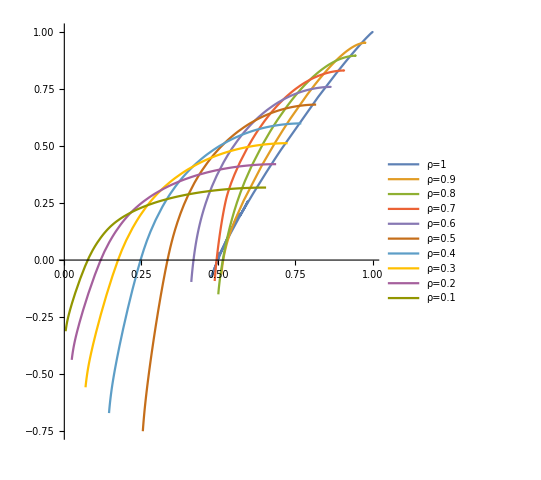

```mathematica
ParametricPlot[fαs,{q,0,20},AspectRatio->1.2,PlotRange->All,PlotLegends->("ρ="<>ToString[#]&/@{1,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1})]
```

## Theoretical implicit equation for τ_q, f-α

```mathematica
ω=(√5-1)/2//N;
(* interference factor *)
gam[ρ_,q_]:=1/(1+ρ^q);
(* molecular and atomic renormalization factors *)
lambp[ρ_]:=2+gam[ρ,1.] ρ^2;
barlambp[ρ_]:=1+2 ρ^2;
(* q-weights for molecular and atomic levels *)
(* doesn't work; check theoretical expression! *)
Cm[q_,τq_,ρ_]:=((2+(3-2ω)gam[ρ,q] ρ^(2q))+gam[ρ,q] ρ^(2q)(ω^3/barlambp[ρ]^q ω^3 ρ^(-2τq)-(4 ω^2)/lambp[ρ]^q ω^2(ρ/2)^-τq))ω^2(ρ/2)^-τq;
Ca[q_,τq_,ρ_]:=((1+2 ρ^(2q)+(3-2ω)ρ^(4q))+ρ^(4q)(ω^3/barlambp[ρ]^q ω^3 ρ^(-2τq)-(4 ω^2)/lambp[ρ]^q ω^2(ρ/2)^-τq))ω^3 ρ^(-2τq);
(* implicit equation for the fractal dimensions *)
eq[q_,τq_,ρ_]:=(2 ω^2)/lambp[ρ]^q Cm[q,τq,ρ]+ω^3/barlambp[ρ]^q Ca[q,τq,ρ]-1;
eq[q_,τq_,ρ_]:=(4(1+ρ^(2q)/2))/((2+ρ^2)^q)ω^2(ρ/2)^-τq+(1(1+2 ρ^(2q)))/((1+2 ρ^2)^q)ω^3 ρ^(-2τq)-1;
(* find Subscript[τ, q] solving the implicit equation *)
implicitTau[q_,ρ_]:=τ/.FindRoot[eq[q,τ,ρ],{τ,q-1}];
```

## Theoretical prediction for τ_q, f-α

```mathematica
legendreTh[ρ_,qmin_,qmax_]:=Block[{τinterp,α},
τinterp=Interpolation[Table[{q,implicitTau[q,ρ]},{q,qmin,qmax,.01}]];
α[q_]:=τinterp'[q];
{α[q],q α[q]-τinterp[q]}
]
```

```mathematica
fα01th=legendreTh[0.1,-10,20];
```

```mathematica
fα02th=legendreTh[0.2,-10,20];
```

```mathematica
fα03th=legendreTh[0.3,-10,20];
```

```mathematica
fα04th=legendreTh[0.4,-10,20];
```

```mathematica
fα05th=legendreTh[0.5,-10,20];
```

```mathematica
fαpython01=legendre[τpython01];
fαpython05test=legendre[τpython05test];
```

```mathematica
fα01=legendre[τq01];
```

```mathematica
numdat=(fα01/.q->#)&/@Range[0,10,0.25];
```

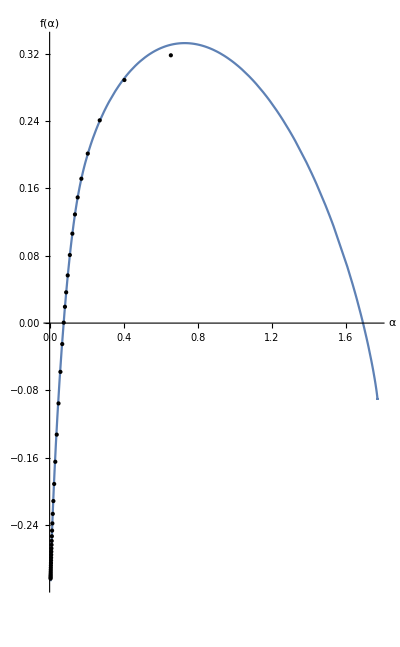

```mathematica
ParametricPlot[fα01th,{q,-10,10},AspectRatio->GoldenRatio,PlotRange->All,AxesLabel->{"α","f(α)"},Epilog->{PointSize[Medium],Point@numdat}]
```

```mathematica
Export[NotebookDirectory[]<>"data/falpha_ldos_rho_01.pdf",%]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/data/falpha_ldos_rho_01.pdf

## Generating various plots

```mathematica
dq=MapThread[{#1,#2/(#1-1)}&,Transpose[τq01]];
```

```mathematica
dqinterp=Interpolation[dq];
dqdat=Table[{q,dqinterp[q] },{q,0,20,0.3}];
```

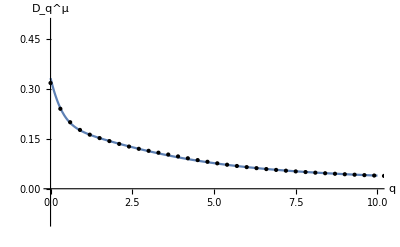

```mathematica
Plot[implicitTau[q,0.1]/(q-1),{q,0.,10.},Epilog->{PointSize[Medium],Point@dqdat},PlotRange->{{0.,10},{-0.1,0.5}},AxesLabel->{"q","D_q^μ"}]
```

```mathematica
Export[NotebookDirectory[]<>"data/average_local_spectral_dimension_ρ_10.pdf",%]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/data/average_local_spectral_dimension_ρ_10.pdf